Coupled Fluid-Field Model

Initializepaclet:PT2GW/tutorial/CoupledFluid-FieldModel#1107461289 | Gravitational wavespaclet:PT2GW/tutorial/CoupledFluid-FieldModel#2089249651
SearchPotentialpaclet:PT2GW/tutorial/CoupledFluid-FieldModel#695896606 | Parameter scanpaclet:PT2GW/tutorial/CoupledFluid-FieldModel#1761326485
PT2GW Internal functionspaclet:PT2GW/tutorial/CoupledFluid-FieldModel#2035979618 | Load/Save datapaclet:PT2GW/tutorial/CoupledFluid-FieldModel#1779242395

Example notebook for the coupled fluid-scalar field (CFF) model defined by the potential
	V(ϕ,T) =  γ/2 (T^2-T0^2) ϕ^2 - A/3 T ϕ^3 + λ/4 ϕ^4 .
The model is widely used for numerical simulations of cosmological phase transitions, see arXives 1504.03291 (https://arxiv.org/abs/1504.03291), 9309059 (https://arxiv.org/abs/astro-ph/9309059), and references therein.
After loading an instance of the CFF model, this notebook illustrates a quick implementation of PT2GW's  wrapping function SearchPotential.
We then elaborate on its internal functions and the GW sub-package, computing gravitational wave spectra. Finally, we implement a simple parameter-scan and illustrate how to save/load benchmarks and transitions.

Please cite arXiv 2505.04744https://arxiv.org/abs/2505.04744 if the analysis you perform with PT2GWFinder results in a publication.

CFFModelpaclet:PT2GW/ref/CFFModelPT2GW Package Symbol | Coupled fluid-field model, including a few benchmarks and Transitionpaclet:PT2GW/ref/TransitionPT2GW Package Symbols.
SearchPotentialpaclet:PT2GW/ref/SearchPotentialPT2GW Package Symbol | runs the full BSM → GW pipeline for a given temperature-dependent scalar potential and bubble wall velocity ξ_w.
SearchPhasespaclet:PT2GW/ref/SearchPhasesPT2GW Package Symbol | finds first order phase transitions(if any) and derive associated gravitational wave spectra from a given particle physics potential V and two phases ϕ_(1,2)

Load the PT2GW package

```mathematica
<< PT2GW`
```

Initialize

Load the Models package:

```mathematica
<< PT2GW/Models.m
```

✓ Imported Models`

The  coupled fluid-field model is defined by the potential

```mathematica
CFFModel[][ϕ,T]
```

1/2 γ (-T0^2+T^2) ϕ^2-1/3 A T ϕ^3+(λ ϕ^4)/4

Load the nth benchmark

```mathematica
idx=1;
V=CFFModel[idx];
V[ϕ,T]
```

0.0277778 (-19600.+T^2) ϕ^2-0.0146402 T ϕ^3+0.00385802 ϕ^4

### Define parameters

Define bubble wall velocity

```mathematica
vw=.9 (* units of c *)
```

0.9

#### Auxiliary parameters

Define energy units (defaults to GeV), belonging to the

field

temperature

Planck mass (entering the Hubble parameter)

```mathematica
DefineUnits["GeV"]
```

Energy units set to  1 GeV

Number of relativistic degrees of freedom (defaults to SM value at the electroweak scale)

```mathematica
RelativisticDOF=106.75; (* RelativisticDOF is a PT2GW package variable *)
```

Optional: define data required to compute the bubble wall collision efficiency κcol

```mathematica
(* this is the minimal data necessary to compute Subscript[κ, col] *)
colData = {"GaugeCouplings" -> {0.1}, "MassFunctions" -> {"Bosons" -> {MassFunction[V]}}, "T0" -> "Tn", "T" -> "Tp"};
```

```mathematica
(* alternatively, one may define directly Subscript[κ, col] *)
(* colData={"κcol"->0.1} *)
```

SearchPotential

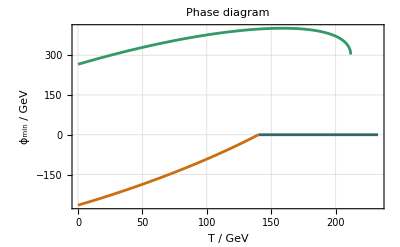

Looping over pairs of phases

Found transition at critical temperature

T_c  →  197.99 GeV

Computing nucleation temperature via Γ/H^4≈1 criterion and Bisection method...

T_n^estimate  →  170.703 GeVS_3/T → 148.609Γ/H^4 → 1.00114

Fitting action...

Action function →  ActionFunction[…]

T_n  →  170.052 GeVS_3/T → 140.957Γ/H^4 → 1979.15∫_T_n^T_c ⅆT/TΓ/H^4 → 0.999899

Computing phase transition parameters...

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

T_p  →  168.365 GeV

Percolation condition:  satisfied (-2.3443×10^-11)

T_transition →  Tp

α →   0.00154779

β/H →   1677.1

No GWs from bubble collisions: κ_col is Indeterminate. 
    Collisions' efficiency must be provided or computed via mass functions.

f^peak  →  0.0193534 Hz

h^2Ω_GW^peak →   1.11649×10^-20

Transition →  Transition[…]

```mathematica
transitions=SearchPotential[V,vw,
	"TracingMethod"->NSolve,
	"CollisionData"->None (* colData *),
	"Metadata"->CFFModel[idx,"Benchmark"]//Normal (* optional: include metadata. Here we include the benchmark parameters. *),
	"Plots"->{"PhaseDiagram"}
	(* NB Plots may cause Dynamic Updating issues while computing:
	avoid hovering over plots, or switch off Dynamic Updating *)
	];//EchoTiming
```

33.8945

To run a search for phase transitions, it is sufficient to provide the potential and bubble wall velocity

### Inspect transition

Extract  transition  from  list

```mathematica
tr=transitions[[1]]
AutoComplete[tr]; (* optional: quickly search keys from a drop-down menu *)
```

Transition[…]

Inspect transition elements

```mathematica
tr["ActionFunction"]
```

ActionFunction[…]

The  key - search  for  Transitions  behaves  like the built-in  Lookup

```mathematica
tr[{"α","β/H","not a key"},"missing",Log10]
```

{-2.81029,3.22456,missing}

Display all data as Dataset

```mathematica
tr//Dataset
```

Get the underlying Association

```mathematica
tr//Normal
```

### Plots

Plot a phase diagram for the transition

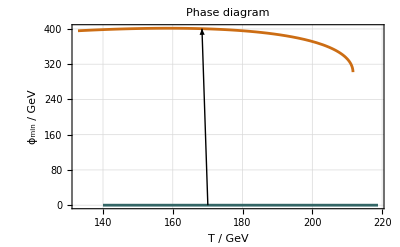

```mathematica
PlotTransition[tr]
```

The action vs temperature, and the transition milestones

```mathematica
PlotAction[tr]
```

-Graphics-

The gravitational wave spectra

```mathematica
PlotGW[tr]
```

-Graphics-

PT2GW Internal functions

All PT2GWFinder functions feature usage messages

```mathematica
?SearchPhases
```

A   template  for  the  function  arguments  can  be  pasted  from  the  popup  menu  (Ctrl + Shift + K, Cmd + Shift + K  on  Mac)

```mathematica
SearchPhases[V,{Subscript[ϕ, 1],Subscript[ϕ, 2]},Subscript[ξ, w]]
```

To  list  all  PT2GW  functions , use

```mathematica
?PT2GW`*
```

In the following, we may either use the transition object computed in SearchPotential, or load it from the examples:

```mathematica
tr=CFFModel[idx,"Transition"]
AutoComplete[tr];
```

Transition[…]

### Potential

Plot the potential, with dynamic temperature and field ranges

```mathematica
PlotPotential[V,2 10.^2{-1,3},100.,"LogTRange"->2.5,"LogϕRange"->1.]
```

-Graphics-

Add sliders for the potential parameters

```mathematica
pot[ϕ_,T_,{γ_,A_,λ_,T0_}]:=CFFModel[][ϕ,T]/.{"γ"->γ,"A"->A,"λ"->λ,"T0"->T0}
```

```mathematica
Manipulate[Plot[pot[ϕ,T,{γ,A,λ,T0}],{ϕ,-ϕrange,2ϕrange}],
{{ϕrange,10^3},10,10^4},
{{T,200.},100.,300.},
{{γ,"γ"},0.,.5},
{{A,"A"},0.,.1},
{{λ,"λ"},0.,.1},
{{T0,"T0"},0.,200.}
]/.Normal[CFFModel[3,"Benchmark"]]//N
```

-Graphics-

### Phase tracing

Trace the phases semi-analytically with NSolve:

```mathematica
Phases=TracePhases[V,"TracingMethod"->NSolve]//
Echo[#,"Phases →",TableForm]&;
```

-Graphics-

Phases →  Function[T,ConditionalExpression[0, 140.<T<211.66||T>211.66]]
Function[T,ConditionalExpression[1.42302 T-2.44377×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.]]
Function[T,ConditionalExpression[1.42302 T+2.44377×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.||140.<T<211.66]]

```mathematica
(* alternatively, use numerical methods *)
(*Phases=TracePhases[V,"TracingMethod"->"Numeric","TRange"->{0,300}]//
Echo[#,"Phases →",TableForm]&;*)
```

Only the  1st and 3rd phase feature a transition with a temperature overlap

```mathematica
With[{phaseCouples=Subsets[Phases,{2}]},
	FindCritical[V,#]&/@phaseCouples//
	TableForm[#,TableHeadings->{Subsets[Range[Length[Phases]],{2}]}]&
	]
```

{1,2} | None
{1,3} | 197.99
{2,3} | None

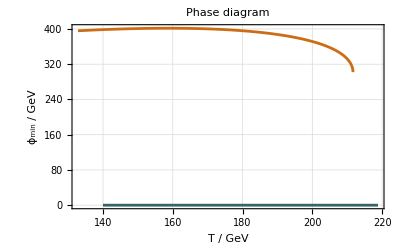

```mathematica
PlotPhases[tr["Phases"]]
```

### ActionFit

Compute  action (calling FindBounce)

```mathematica
Action[tr["Tn"],V,tr["Phases"]]
```

140.957

Compute  Euclidean  action  (calling  FindBounce)  and  fit  the  action - temperature  function S_ 3/T  (T)

```mathematica
actionFunction=ActionFit[V,tr["Phases"],{145.,180.},tr["Tc"],
	"Data"->None (*actionFunction["Data"]optional: pass action data if already computed *),
	"Orders"->Range[-2,1] (* set the orders used in the Laurent polynomial fit function: ∑_n c_n(Tc-T)^n *)
	]
```

ActionFunction[…]

Compare fit functions

```mathematica
fits=Table[ActionFit[V,tr["Phases"],actionFunction["Domain"],tr["Tc"],"Data"->actionFunction["Data"],options],{options,{
	{},
	{"Orders"->Range[-3,0]},
	{"ActionMethod"->Interpolation}
	}}];
LogPlot[Through[Through[fits["Function"]][T]]//Evaluate,{T,149.,198.},
	PlotStyle->{Dashing[None],Dashed,Dashed},
	PlotLegends->{"default","orders→(-3,0)","\"ActionMethod\"→Interpolation"},
	GridLines->Automatic
	]
```

-Graphics-

### Nucleation temperature

Compute the nucleation rate

```mathematica
DecayRate[tr["Tn"],V,tr["Phases"]]
```

5.39234×10^-51

Plot  Γ/H^4 (T)

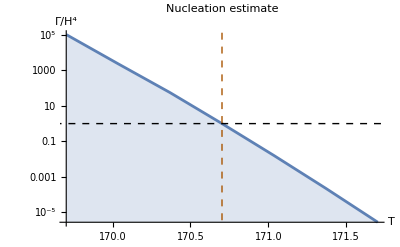

```mathematica
DiscretePlot[DecayOverHubble[T,V,tr["Phases"]],{T,Subdivide[tr["TnEstimate"]-1,tr["TnEstimate"]+1,6]},
	AxesLabel->{"T","Γ/\!\(\*SuperscriptBox[\(H\), \(4\)]\)"},PlotLabel->"Nucleation estimate",
	"ScalingFunctions"->"Log",Joined->True,
	Epilog->{Dashed,InfiniteLine[{0,Log@1},{1,0}],Darker@Orange,InfiniteLine[{tr["TnEstimate"],1},{0,1}]}
	]
```

Plot the nucleation criterion integral (requires the action function)

```mathematica
actionFunction=tr["ActionFunction"]
```

ActionFunction[…]

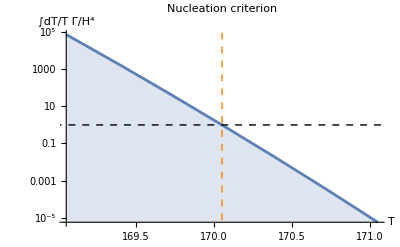

```mathematica
DiscretePlot[IntegralDecay[T,tr["Tc"],actionFunction["Function"],V,tr["Phases"]],{T,Subdivide[tr["Tn"]-1,tr["Tn"]+1,6]},
AxesLabel->{"T","∫dT/T Γ/\!\(\*SuperscriptBox[\(H\), \(4\)]\)"},PlotLabel->"Nucleation criterion",
"ScalingFunctions"->"Log",Joined->True,Epilog->{Dashed,InfiniteLine[{0,Log@1},{1,0}],Orange,InfiniteLine[{tr["Tn"],1},{0,1}]}]
```

Estimate nucleation temperature

```mathematica
(* bisection method on Γ/H^4≈1 criterion (default) *)
FindNucleation[V,{140.,180.},tr["Phases"],"PrintIterations"->False,
	Return->{"Tn","NucleationDecayOverHubble"}
	(*"NucleationCriterion"->{"ActionValue"->140.}*)
	]//EchoTiming
```

6.95929

{170.702,1.01115}

For the CFF model, the nucleation can be estimated analytically, by expanding the action around

the critical temperature Tc, and

the inflection point T0

```mathematica
TnEst=NucleationCFF[V,140.] (* S_3/T≈140. for a transition at the EW scale *)
```

Expansion accuracies:  T_0 → 23.15%
T_c → 61.24%

Selecting expansion around Tc

168.08

```mathematica
SearchPotential[V,vw=.9,"TnEstimate"->TnEst,"TracingMethod"->NSolve]
```

Looping over pairs of phases

Found transition at critical temperature

T_c  →  197.99 GeV

T_n^estimate  →  168.08 GeVS_3/T → 119.684Γ/H^4 → 2.80649×10^12

Fitting action...

Action function →  ActionFunction[…]

T_n  →  170.065 GeVS_3/T → 141.111Γ/H^4 → 1982.25∫_T_n^T_c ⅆT/TΓ/H^4 → 0.999999

Computing phase transition parameters...

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

T_p  →  168.362 GeV

Percolation condition:  satisfied (-2.31432×10^-11)

T_transition →  Tp

α →   0.00154792

β/H →   1674.48

No GWs from bubble collisions: κ_col is Indeterminate. 
    Collisions' efficiency must be provided or computed via mass functions.

f^peak  →  0.0193227 Hz

h^2Ω_GW^peak →   1.11863×10^-20

Transition →  Transition[…]

{Transition[…]}

Compute precise value with integral nucleation criterion

```mathematica
(* integral decay criterion, requiring action function *)
FindNucleation[V,{140.,180.},tr["Phases"],"PrintIterations"->True,
	"NucleationCriterion"->"IntegralDecay",
	"NucleationMethod"->{"ActionFunction"->tr["ActionFunction"]["Function"],"Tc"->tr["Tc"],"TnEstimate"->tr["TnEstimate"]},
	Return->"Tn"
	(*"NucleationCriterion"->{"ActionValue"->140.}*)
	]//EchoTiming
```

0.076966

170.052

### Percolation temperature

Plot I_F=-log(P_F), where P_F is the false-vacuum fractional volume (requires the action function).
The percolation temperature corresponds to I_F(T_p)≃0.34.

```mathematica
actionFunction=tr["ActionFunction"]
```

ActionFunction[…]

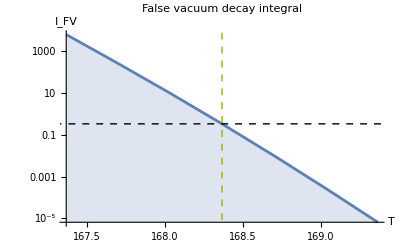

```mathematica
DiscretePlot[IntegralFalseVacuum[actionFunction["Function"],T,tr["Tc"],vw,V,tr["Phases"]],
	{T,Subdivide[tr["Tp"]-1,tr["Tp"]+1,6]},
	AxesLabel->{"T","\!\(\*SubscriptBox[\(I\), \(FV\)]\)"},PlotLabel->"False vacuum decay integral",
	"ScalingFunctions"->"Log",Joined->True,
	Epilog->{Dashed,InfiniteLine[{0,Log@.34},{1,0}],Darker@Yellow,InfiniteLine[{tr["Tp"],1},{0,1}]}
	]
```

Determine  the  percolation  temperature  by  solving  I_F(T_p) = 0.34

```mathematica
FindPercolation[actionFunction["Function"], {tr["Tn"], tr["Tc"]}, vw, V, tr["Phases"]]
```

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

168.365

### Transition parameters

Compute the transition strength α

```mathematica
Alpha[tr["Tp"], V, tr["Phases"]]
Echo[tr["α"], "precomputed →"];
```

0.00154779

precomputed →  0.00154779

Compute the inverse duration in Hubble units β/H(T*)

```mathematica
BetaHubble[tr["Tp"],tr["ActionFunction"]["Function"]]
Echo[tr["β/H"],"precomputed →"];
```

1677.1

precomputed →  1677.1

### SearchPhases

Search for phase transitions given a potential and two of its phases

```mathematica
Phases=TracePhases[V,"TracingMethod"->NSolve]
phases=Phases[[{1,3}]];
```

-Graphics-

{Function[T,ConditionalExpression[0, 140.<T<211.66||T>211.66]],Function[T,ConditionalExpression[1.42302 T-2.44377×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.]],Function[T,ConditionalExpression[1.42302 T+2.44377×10^-9 √(1.18151×10^22-2.63729×10^17 T^2), 0<T<140.||140.<T<211.66]]}

SearchPhases wraps the functions above:

FindCritical

ActionFit

FindNucleation

FindPercolation

and computes the GW spectra

```mathematica
tr=SearchPhases[V,phases,vw,
	"NActionPoints"->31, (* set the number of computations of the action *)
	"CollisionData"->None (* colData *),
	"Metadata"->CFFModel[idx,"Benchmark"]//Normal, (* include meta data: here, we save the benchmark parameters *)
	"Plots"->{"PhaseDiagram"(* ,"Action" *)(* ,"GW" *)},
	ProgressIndicator->True
];//EchoTiming
```

Found transition at critical temperature

T_c  →  197.99 GeV

Computing nucleation temperature via Γ/H^4≈1 criterion and Bisection method...

T_n^estimate  →  170.703 GeVS_3/T → 148.609Γ/H^4 → 1.00114

Fitting action...

Action function →  ActionFunction[…]

T_n  →  170.052 GeVS_3/T → 140.957Γ/H^4 → 1979.15∫_T_n^T_c ⅆT/TΓ/H^4 → 0.999899

Computing phase transition parameters...

Solving I_ℱ(T_p) = 0.34 for T_p with FindRootpaclet:ref/FindRoot method...

T_p  →  168.365 GeV

Percolation condition:  satisfied (-2.3443×10^-11)

T_transition →  Tp

α →   0.00154779

β/H →   1677.1

No GWs from bubble collisions: κ_col is Indeterminate. 
    Collisions' efficiency must be provided or computed via mass functions.

f^peak  →  0.0193533 Hz

h^2Ω_GW^peak →   1.1165×10^-20

29.2532

```mathematica
AutoComplete[tr]; (* optional: quickly access Transition keys from a drop-down menu *)
```

Gravitational waves

To compute the GW spectra from a set of phase transition parameters, we first load a Transition object
(this already contains GW spectral parameters, but we will recompute them)

```mathematica
V=CFFModel[idx=1]
tr=CFFModel[idx,"Transition"]
AutoComplete[tr];
```

Function[{ϕ$,T$},0.0277778 (-19600.+T$^2) ϕ$^2-0.0146402 T$ ϕ$^3+0.00385802 ϕ$^4]

Transition[…]

### Compute GW spectra

ComputeGW is defined in the GW` sub-package. It computes  GW spectra, requiring the following transition parameters:

```mathematica
ComputeGW[T,α,"β/H",Subscript[ξ, w],g,$Unit]
```

When a Transition (or Association) object is passed as argument, the parameters are automatically extracted.
NB Missing arguments given an error:

```mathematica
ComputeGW[KeyDrop[tr//Normal,"α"]]//Dataset
```

Missing {α} in input Association.
SGWB cannot be computed!

$Aborted

ComputeGW  returns  an  Associationpaclet:ref/Association  of  GW  parameters, and  stores  it  in  the  GWData symbol, from the GW` sub-package

```mathematica
ComputeGW[tr//Normal]//Dataset
```

No GWs from bubble collisions: κ_col is Indeterminate. 
    Collisions' efficiency must be provided or computed via mass functions.

The  spectra, corresponding to the key "h2Omega", can be plotted with PlotGW

```mathematica
PlotGW[GWData["h2Omega"]]
```

-Graphics-

### Collision efficiency κcol

To add the contribution from bubble wall collisions, we must include, to the least, the following information:
• a bosonic mass function
• a gauge coupling value
• characteristic temperatures for bubble growth, T0 and T* (see 1903.09642)

```mathematica
(* MassFunction is just the square root of the second field-derivative: ∂_ϕ^2 V(ϕ,T) *)
mϕ=MassFunction[V];
mϕ[ϕ,T]
```

√(0.0555556 (-19600.+T^2)-0.087841 T ϕ+0.0462963 ϕ^2)

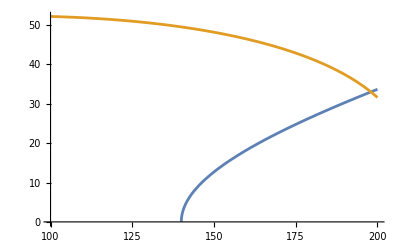

```mathematica
Plot[mϕ[#[T], T] & /@ tr["Phases"] // Evaluate, {T, 100, 200}]
```

The minimal collision data is then

```mathematica
colData={"GaugeCouplings"->{0.1},"MassFunctions"->{"Bosons"->{mϕ}},"T0"->tr["Tn"],"T"->tr["Tp"]};
```

Finally, to compute κcol we must include the transition parameters and potential

```mathematica
data=Append[KeyDrop[tr[Association],"κcol"],colData~Join~{"Potential"->V}];
```

kappaCollision returns the collision efficiency and, optionally, the transition parameters computed along the way

```mathematica
kappaCollision[data,Return->{"κcol","Data"}]//Dataset
```

To compute the contribution from collisions, pass the collision data (including the potential) to the  option "CollisionData":

```mathematica
ComputeGW[tr//Normal,"CollisionData"->colData~Join~{"Potential"->V}]//Dataset
```

### Detector sensitivities

Several peak-integrated (PISCs) and power-law-integrated sensitivity curves (PLISCs) are built-in PT2GW:

```mathematica
PlotGWSensitivities[10^{-9,4},All]
```

-Graphics-

To add a user-defined detector sensitivity, simply  define the corresponding PISC (peak-integrated sensitivity curve), as a function of frequency in Hertz

```mathematica
GWSensitivities[f_, "myDetector", OptionsPattern[]] := 10^-23 (10^3 f^3 + 10^-3 f^-3)
```

```mathematica
PlotGW[tr,"Detectors"->{"LISA PISC","myDetector"}]
```

-Graphics-

Parameter scan

We may run simple parameter scans, optionally exploiting parallelization (see sub-section below).

To  construct  a  Dataset  of  transitions, we  first  define  a  function  to  run  single  a  benchmark  with  option  Dataset -> True, and  append  it  to  a  dataset  DS .

```mathematica
(* suppress the printing of computation status *)
$PT2GWPrint=False;
```

```mathematica
(* separation string *)
sep=StringRepeat["□■",30];
```

```mathematica
(* run a benchmark and add the found transitions to DataFrame *)
Options[run]={Print->True,EchoTiming->True};
run[benchmarkValues_,opt:OptionsPattern[]]:=Module[{},
	If[!MatchQ[DS,_Dataset],DS=Dataset[{}]];
	If[OptionValue[Print],Print@sep];
	Echo[KeyTake[benchmarkValues,{"T0","γ","A","λ"}],"Running CFF model at →"];
	V=CFFModel[]/.benchmarkValues;
	ds=SearchPotential[V,"WallVelocity"/.benchmarkValues,
		Dataset->True,
		opt,
		"TracingMethod"->NSolve,
		"CollisionData"->benchmarkValues["CollisionData"],
		"Metadata"->KeyTake[benchmarkValues,{"T0","γ","A","λ"}],
		"Plots"->None,
		ProgressIndicator->False
		]//If[OptionValue[EchoTiming],EchoTiming,Identity];
	If[ds=!=Dataset[{}],DS=DS~Join~ds[{1},CFFModel[1,"Transition"][Keys]]]
	]
```

Here, we run the benchmark parameters stored in CFFModel[All,"Benchmark"]
The following command should take a few minutes to evaluate

```mathematica
DS=.;
Scan[Quiet[run[#]]&,
	CFFModel[All,"Benchmark"]//Normal
	]//EchoTiming
```

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running CFF model at →  <|T0→140,γ→1/18,A→(√(5/2))/36,λ→5/324|>

27.8171

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running CFF model at →  <|T0→140,γ→2/9,A→(√10)/9,λ→20/81|>

39.0126

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running CFF model at →  <|T0→140,γ→1/9,A→(√(5/2))/72,λ→0.00192901|>

55.2093

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running CFF model at →  <|T0→50 √2,γ→1/18,A→(√(5/2))/36,λ→5/324|>

32.1381

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running CFF model at →  <|T0→50 √2,γ→1/9,A→(√(5/2))/36,λ→5/648|>

64.6505

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running CFF model at →  <|T0→140,γ→1/9,A→(√(5/2))/72,λ→0.00192901|>

59.9918

279.083

With the Dataset format, it is easy to compare the parameters of different transitions

```mathematica
DS
```

Alternatively, we may obtain a list of Transition objects with Table.
Here we recompute the transitions above, corresponding to the ones stored in CFFModel[All,"Transition"]
The following command should take a few minutes to evaluate.

```mathematica
transitions=Table[
With[{benchmarkValues=CFFModel[n,"Benchmark"]//Normal,V=CFFModel[n]},
	Print[sep];
	Echo[KeyTake[benchmarkValues,{"T0","γ","A","λ"}],"Running benchmark →"];
	RelativisticDOF="RelativisticDOF"/.benchmarkValues;
	SearchPotential[V,"WallVelocity"/.benchmarkValues,"TracingMethod"->NSolve,
	"CollisionData"->benchmarkValues["CollisionData"],
	"Metadata"->KeyTake[benchmarkValues,{"T0","γ","A","λ"}],
	"Plots"->None,
	ProgressIndicator->False
	]//Quiet//EchoTiming 
	],
{n,Length@CFFModel[All,"Benchmark"]}]//Flatten
```

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running benchmark →  <|T0→140,γ→1/18,A→(√(5/2))/36,λ→5/324|>

38.4965

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running benchmark →  <|T0→140,γ→2/9,A→(√10)/9,λ→20/81|>

59.3407

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running benchmark →  <|T0→140,γ→1/9,A→(√(5/2))/72,λ→0.00192901|>

57.9305

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running benchmark →  <|T0→50 √2,γ→1/18,A→(√(5/2))/36,λ→5/324|>

36.2154

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running benchmark →  <|T0→50 √2,γ→1/9,A→(√(5/2))/36,λ→5/648|>

67.3377

□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■□■

Running benchmark →  <|T0→140,γ→1/9,A→(√(5/2))/72,λ→0.00192901|>

60.4863

{Transition[…],Transition[…],Transition[…],Transition[…],Transition[…],Transition[…]}

Similarly, we may inspect selected transition parameters

```mathematica
With[{labels={"Tc","Tn","Tp","α","β/H","fPeak","h2OmegaPeak"}},
Through[transitions[ labels]]//TableForm[#,TableHeadings->{Automatic,labels}]&]
```

| Tc | Tn | Tp | α | β/H | fPeak | h2OmegaPeak
1 | 197.99 | 170.259 | 168.584 | 0.00479797 | 1700.81 | 0.0162737 | 5.25563×10^-19
2 | 197.99 | 188.887 | 188.019 | 0.00293356 | 4021.28 | 0.0428921 | 2.16837×10^-20
3 | 197.99 | 147.996 | 147.259 | 0.263512 | 3951.14 | 0.0349818 | 7.00003×10^-15
4 | 100. | 86.0131 | 85.1697 | 0.00153774 | 1707.16 | 0.00996561 | 1.06869×10^-20
5 | 100. | 80.0508 | 79.3257 | 0.0164346 | 1866.29 | 0.0101847 | 1.14286×10^-17
6 | 197.99 | 147.996 | 147.259 | 0.263512 | 3951.09 | 0.0349814 | 7.00019×10^-15

### Parallelization

Use the built-in Parallelize function to launch multiple benchmarks on different kernels.
First, let's set up the parallel kernels

```mathematica
ParallelNeeds["PT2GW`"]
```

```mathematica
(* load PT2GW and the Examples on all kernels *)
ParallelEvaluate[
	<<PT2GW/Models.m;
	$PT2GWPrint=False;
	];
```

```mathematica
(* share between kernels the Dataset container for the transitions *)
SetSharedVariable[DS]
```

```mathematica
(* define a grid of scanning parameters *)
scanParameters=With[{n=5},
	Table[<|"T0"->140.,"γ"->1/9.,"A"->A,"λ"->λ,"RelativisticDOF"->RelativisticDOF,"WallVelocity"->0.95|>,
		{A,E^Subdivide[Log@0.02,Log@0.4,n]},
		{λ,E^Subdivide[Log@0.01,Log@0.25,n]}
	]]//Flatten;
```

```mathematica
(* empty DS *)
DS=.
```

The following command should take a few minutes to evaluate.

```mathematica
(* run parameters in parallel *)
Parallelize@Scan[Quiet[run[#,Print->False,EchoTiming->False]]&,
	scanParameters
	]//EchoTiming;
```

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.02,λ→0.01|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.02,λ→0.036239|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.02,λ→0.131326|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0364113,λ→0.01|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0364113,λ→0.036239|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0364113,λ→0.131326|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0662891,λ→0.01|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0662891,λ→0.036239|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0662891,λ→0.131326|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0662891,λ→0.25|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.120684,λ→0.01|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.120684,λ→0.0190365|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.120684,λ→0.036239|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.120684,λ→0.0689865|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.120684,λ→0.131326|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.120684,λ→0.25|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0662891,λ→0.0689865|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.219712,λ→0.01|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.219712,λ→0.0190365|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.219712,λ→0.036239|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.219712,λ→0.0689865|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.219712,λ→0.131326|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.219712,λ→0.25|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.4,λ→0.01|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.4,λ→0.0190365|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.4,λ→0.036239|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.4,λ→0.0689865|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.4,λ→0.131326|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.4,λ→0.25|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0364113,λ→0.0689865|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.02,λ→0.0689865|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.02,λ→0.0190365|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0662891,λ→0.0190365|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.02,λ→0.25|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0364113,λ→0.0190365|>

Running CFF model at →  <|T0→140.,γ→0.111111,A→0.0364113,λ→0.25|>

209.088

Visualize scan results

```mathematica
DS
```

```mathematica
(* plot the scanning and transition parameters *)
With[{scanParams={"λ","A"},tranParams={"α","β/H"}},
	PointValuePlot[(scanParams->Log10[tranParams])/.Normal[DS],
		{1->"Color",2->"Size"},
		ScalingFunctions->{"Log","Log"},
		PlotLegends->Automatic,
		FrameLabel->scanParams
		]/.BarLegend[x___]:>BarLegend[x,LegendLabel->StringTemplate["log(``)"]@tranParams[[1]]]
	]
```

-Graphics-

```mathematica
(* reproduce plot from the paper *)
Module[{scanParams={"λ","A"},tranParams={"α","β/H"},grid=Automatic,font={FontSize->8,FontFamily->"Latin Modern Math"}},
	grid=DeleteDuplicates[DS[All,#]//Normal]&/@scanParams;
	Row[PointValuePlot[(scanParams->Log10[#])/.Normal[DS],
		{1->"Color",2->"Size"},
		PlotRangePadding->{{.2,.4},{.15,.35}},
		PlotStyle->PointSize[.04],
		ScalingFunctions->{"Log","Log"},
		ColorFunction->(#/.{"α"->ColorData[{"RedBlueTones","Reverse"}],_->"RedBlueTones"}),
		PlotLegends->Automatic,
		ImageSize->200,
		GridLines->grid,
		Frame->True,
		AspectRatio->1,
		FrameLabel->scanParams
		]/.BarLegend[x___]:>BarLegend[x,LegendLabel->
		StringTemplate["\!\(\*SubscriptBox[\(log\), \(10\)]\) ``"][#]]&/@tranParams[[All]],
		Spacer[0]]]
```

-Graphics-

Load/Save data

### Load the coupled fluid-field model

The CFFModel is defined as

```mathematica
CFFModel[][ϕ,T]
```

1/2 γ (-T0^2+T^2) ϕ^2-1/3 A T ϕ^3+(λ ϕ^4)/4

You  can load specific benchmarks by passing an index argument

```mathematica
idx=3;
V=CFFModel[idx];
V[ϕ,T]
```

To list the default benchmark parameters, use the "Benchmark" argument

```mathematica
CFFModel[All,"Benchmark"]
```

Benchmark parameters can be defined as Associations

```mathematica
bp=<|"T0"->140,"γ"->1/18,"A"->Sqrt[5/2]/36,"λ"->5/324|>;
V=CFFModel[]/.bp
```

### Load a CFF transition

The transitions corresponding to the benchmark parameters above can be loaded with the "Transition" argument

```mathematica
tr=CFFModel[1,"Transition"]
```

Transition[…]

### Store a transition

As an examples, here we save a Transition object to a .m file in the local directory.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tr >> transition_CFF.m
```

The same transition can then be loaded with

```mathematica
tr=<<transition_CFF.m
```

### Store a Dataset

Storing a Dataset is simple:

```mathematica
(* save/load Dataset *)
SetDirectory[NotebookDirectory[]];
Compress[DS]>>CFF_Dataset.m
```

Load the Dataset

```mathematica
Uncompress[<<CFF_Dataset.m]
```

| Related Guides
▪PT2GWFinder

| Related Tech Notes
▪Dark Photon Model - Daisy resummation